```mathematica
NN = 3;
mm  = 1.0;


Subscript[M, 1] = mm ( ⅇ^(2 π ⅈ / NN) - 1. );
Subscript[M, 2]  = mm( ⅇ^(4 π ⅈ / NN) - 1. );
M = Abs[Subscript[M, 1]];
Subscript[μ, 1]    =  (-ⅈ Subscript[M, 1])/(2M);
Subscript[μ, 2]      = (-ⅈ Subscript[M, 2])/(2 M);
f[s_] := ⅇ^s/(1  +  ⅇ^s)
```

```mathematica
Subscript[λ, 1][s_] := Abs[ Subscript[μ, 1] ] f[s]   +   Abs[ Subscript[μ, 2]  -  Subscript[μ, 1] f[s] ]
```

```mathematica
Subscript[λ, 2][s_] := Abs[ Subscript[μ, 1] ] f[s]   -   Abs[ Subscript[μ, 2]  -  Subscript[μ, 1] f[s] ]
```

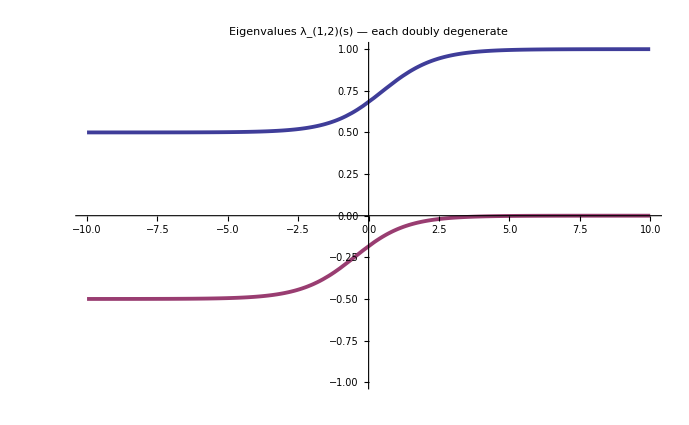

```mathematica
Plot[ { Subscript[λ, 1][s],  Subscript[λ, 2][s] },    { s,  -10, 10 } , PlotStyle->{ Thickness[0.004] }, PlotLabel-> Style ["Eigenvalues λ_(1,2)(s)  —  each doubly degenerate", 22, FontFamily->"Times"],
LabelStyle->Directive[16], PlotRange->{ -1,  1 } ]
```